```mathematica
f[x_]=48 x (1+x)^60 - (1+x)^60 +1
```

1-(1+x)^60+48 x (1+x)^60

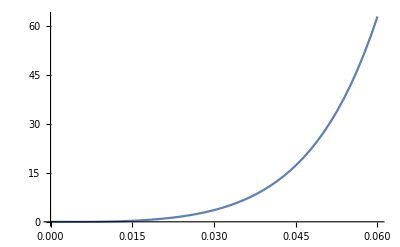

```mathematica
Plot[f[x],{x,0,.06}]
```

```mathematica
FindRoot[f[x],{x,1}]
```

{x→0.0076286}

```mathematica
Newton[x_]=x-f[x]/f'[x]
```

x-(1-(1+x)^60+48 x (1+x)^60)/(-60 (1+x)^59+2880 x (1+x)^59+48 (1+x)^60)

```mathematica
For[i =1; t=.007,i<5,i++,t = Newton[t];Print[N[t]]]
```

0.0077101

0.00762971

0.0076286

0.0076286

-x+Cos[x]

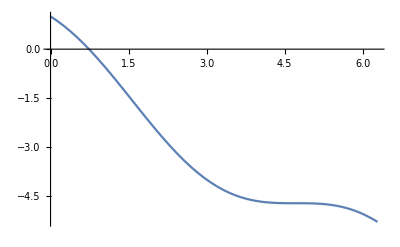

```mathematica
g[x_] = Cos[x]-x
Plot[g[x],{x,0,2 Pi}]
```

```mathematica
Table[{x,g[x]},{x,0,1,.01}]
```

{{0.,1.},{0.01,0.98995},{0.02,0.9798},{0.03,0.96955},{0.04,0.9592},{0.05,0.94875},{0.06,0.938201},{0.07,0.927551},{0.08,0.916802},{0.09,0.905953},{0.1,0.895004},{0.11,0.883956},{0.12,0.872809},{0.13,0.861562},{0.14,0.850216},{0.15,0.838771},{0.16,0.827227},{0.17,0.815585},{0.18,0.803844},{0.19,0.792004},{0.2,0.780067},{0.21,0.768031},{0.22,0.755897},{0.23,0.743666},{0.24,0.731338},{0.25,0.718912},{0.26,0.70639},{0.27,0.693771},{0.28,0.681055},{0.29,0.668244},{0.3,0.655336},{0.31,0.642334},{0.32,0.629235},{0.33,0.616042},{0.34,0.602755},{0.35,0.589373},{0.36,0.575897},{0.37,0.562327},{0.38,0.548665},{0.39,0.534909},{0.4,0.521061},{0.41,0.507121},{0.42,0.493089},{0.43,0.478966},{0.44,0.464752},{0.45,0.450447},{0.46,0.436052},{0.47,0.421568},{0.48,0.406995},{0.49,0.392333},{0.5,0.377583},{0.51,0.362745},{0.52,0.347819},{0.53,0.332807},{0.54,0.317709},{0.55,0.302525},{0.56,0.287255},{0.57,0.271901},{0.58,0.256463},{0.59,0.240941},{0.6,0.225336},{0.61,0.209648},{0.62,0.193878},{0.63,0.178028},{0.64,0.162096},{0.65,0.146084},{0.66,0.129992},{0.67,0.113822},{0.68,0.0975727},{0.69,0.081246},{0.7,0.0648422},{0.71,0.0483619},{0.72,0.0318057},{0.73,0.0151744},{0.74,-0.00153144},{0.75,-0.0183111},{0.76,-0.035164},{0.77,-0.0520893},{0.78,-0.0690865},{0.79,-0.0861547},{0.8,-0.103293},{0.81,-0.120502},{0.82,-0.137779},{0.83,-0.155124},{0.84,-0.172537},{0.85,-0.190017},{0.86,-0.207563},{0.87,-0.225173},{0.88,-0.242849},{0.89,-0.260588},{0.9,-0.27839},{0.91,-0.296254},{0.92,-0.31418},{0.93,-0.332166},{0.94,-0.350212},{0.95,-0.368317},{0.96,-0.38648},{0.97,-0.4047},{0.98,-0.422977},{0.99,-0.44131},{1.,-0.459698}}

```mathematica
Newton[x_]=x-g[x]/g'[x]
For[i =1; t=.7,i<5,i++,t = Newton[t];Print[N[t]]]
```

x-(-x+Cos[x])/(-1-Sin[x])

0.739436

0.739085

0.739085

0.739085

```mathematica
FindRoot[g[x],{x,.7}]
```

{x→0.739085}

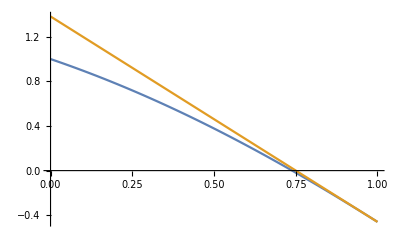

```mathematica
Plot[{g[x],g'[1](x-1)+g[1]},{x,0,1}]
```